## Symmetry set for parametric curves

```mathematica
(*Defining the parametric curve*)
a=1.5;
b=1;
q=20;
H=0.8;
x[t_]:=a Sin[t];
y[t_]:=b (Cos[t]-1)-H*Exp[-q*t^2];
```

```mathematica
(*Define the two equations*)
norm[t_]:=Sqrt[x'[t]^2+y'[t]^2];
unitTangent[t_]:={x'[t],y'[t]}/norm[t];
unitNormal[t_]:=Module[{T=unitTangent[t]},{-T[[2]],T[[1]]}];

(*Function to compute curvature at parameter t*)
computeCurvature[t_,dt_: 1*^-5]:=Module[{dx,dy,ddx,ddy,numerator,denominator},(*First derivatives*)
dx=x'[t];
dy=y'[t];
(*Second derivatives*)
ddx=x''[t];
ddy=y''[t];
(*Curvature formula:κ=(x'y''-y'x'')/(x'^2+y'^2)^(3/2)*)
numerator=dx*ddy-dy*ddx;
denominator=(dx^2+dy^2)^1.5;
If[Abs[denominator]<1*^-10,0.0,numerator/denominator]];

(*Function to compute focal point at parameter t*)
computeFocalPoint[t_,RMax_: 10.0]:=Module[{p,N,kappa,R,focalPoint},p={x[t],y[t]};
N=unitNormal[t];
kappa=computeCurvature[t];
(*If curvature is too small,skip*)
If[Abs[kappa]<1*^-10,Return[Null]];
(*Radius of curvature*)
R=1.0/kappa;
(*If radius is too large,skip*)
If[Abs[R]>RMax,Return[Null]];
(*Focal point is at distance R along the normal*)
focalPoint=p+N*R;
focalPoint];

(*Function to compute all focal set points*)
computeFocalSet[resolution_: 2000,RMax_: 10.0]:=Module[{dt,tValues,focalPoints={},fp},dt=2Pi/resolution;
tValues=Table[-Pi+i*dt,{i,0,resolution}];
Do[fp=computeFocalPoint[t,RMax];
If[fp=!=Null&&!AnyTrue[fp,Not@*NumericQ],AppendTo[focalPoints,fp]];,{t,tValues}];
focalPoints];

(*Compute focal set*)
Print["Computing focal set..."];
focalPoints=computeFocalSet[2000,10.0];
Print["Found ",Length[focalPoints]," focal set points."];

eq1[t1_,t2_]:=({x[t1],y[t1]}-{x[t2],y[t2]}).(unitTangent[t1]+unitTangent[t2]);
eq2[t1_,t2_]:=({x[t1],y[t1]}-{x[t2],y[t2]}).(unitTangent[t1]-unitTangent[t2]);

(*Function to find sign change points for a fixed t1*)
findSignChanges[t1_?NumericQ,dt_: 0.01,lambdaMax_: 3.0,tangentThreshold_: 1*^-5]:=Module[{t2Values,thresholdIdx,signChanges={},prevCheck1=Null,prevCheck2=Null,prevT2=Null,T1,N1,T2,N2,p1,p2,diff,TsumVec,TdiffVec,eqCheck1,eqCheck2,alpha,tInterp,pInterp,NInterp,Nvec,denom,lam,center},(*Generate t2 values from-Pi to Pi*)t2Values=Range[-Pi,Pi,dt];
thresholdIdx=Max[1,Floor[0.05*Length[t2Values]]];
(*Get tangent and normal for t1*)T1=unitTangent[t1];
N1=unitNormal[t1];
p1={x[t1],y[t1]};
(*Loop through t2 values,starting from threshold index*)Do[T2=unitTangent[t2Values[[j]]];
N2=unitNormal[t2Values[[j]]];
p2={x[t2Values[[j]]],y[t2Values[[j]]]};
(*Skip if tangents are parallel or anti-parallel*)If[Norm[T1-T2]<tangentThreshold||Norm[T1+T2]<tangentThreshold,prevCheck1=Null;
prevCheck2=Null;
prevT2=t2Values[[j]];
Continue[]];
(*Compute tangency conditions*)diff=p1-p2;
TsumVec=T1+T2;
TdiffVec=T1-T2;
eqCheck1=diff.TsumVec;
eqCheck2=diff.TdiffVec;
(*Check for sign changes*)If[prevCheck1=!=Null,(*Check eq1 sign change*)If[prevCheck1*eqCheck1<0,alpha=Abs[prevCheck1]/(Abs[prevCheck1]+Abs[eqCheck1]);
tInterp=prevT2+alpha*(t2Values[[j]]-prevT2);
pInterp={x[tInterp],y[tInterp]};
NInterp=unitNormal[tInterp];
Nvec=N1+NInterp;
denom=Nvec.Nvec;
If[Abs[denom]>1*^-8,lam=(pInterp-p1).Nvec/denom;
If[Abs[lam]<lambdaMax,center=p1+lam*N1;
AppendTo[signChanges,{t1,tInterp,"eq1",p1,pInterp,lam,center}]]]];
(*Check eq2 sign change*)If[prevCheck2*eqCheck2<0,alpha=Abs[prevCheck2]/(Abs[prevCheck2]+Abs[eqCheck2]);
tInterp=prevT2+alpha*(t2Values[[j]]-prevT2);
pInterp={x[tInterp],y[tInterp]};
NInterp=unitNormal[tInterp];
Nvec=N1-NInterp;
denom=Nvec.Nvec;
If[Abs[denom]>1*^-8,lam=(pInterp-p1).Nvec/denom;
If[Abs[lam]<lambdaMax,center=p1+lam*N1;
AppendTo[signChanges,{t1,tInterp,"eq2",p1,pInterp,lam,center}]]]]];
(*Update previous values*)prevCheck1=eqCheck1;
prevCheck2=eqCheck2;
prevT2=t2Values[[j]];,{j,thresholdIdx+1,Length[t2Values]}];
signChanges];

(*Scan over all t1 values*)
scanAllT1[dt_: 0.01,lambdaMax_: 3.0,tangentThreshold_: 1*^-5]:=Module[{t1Values,allResults={}},t1Values=Range[-Pi,Pi,dt];
Do[allResults=Join[allResults,findSignChanges[t1val,dt,lambdaMax,tangentThreshold]];,{t1val,t1Values}];
allResults];

(*Run the scan*)
results=scanAllT1[0.01,4.0,1*^-5];

(*Extract centers*)
centers=results[[All,7]];

Print["Found ",Length[centers]," symmetry set points."];
```

Computing focal set...

Found 1989 focal set points.

Found 2070 symmetry set points.

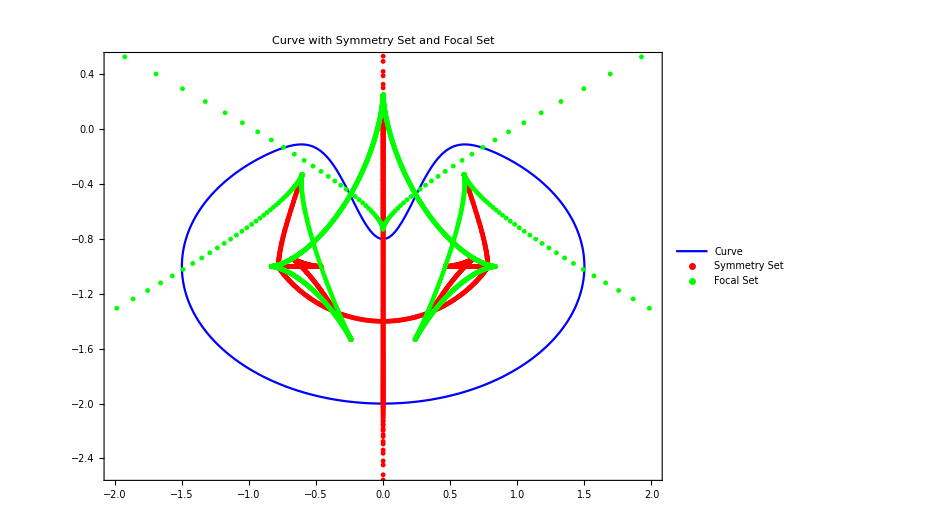

```mathematica
(*Plot*)
Show[ParametricPlot[{x[t],y[t]},{t,-Pi,Pi},PlotRange->{{-2,2},{-2.5,0.5}},PlotStyle->{Blue,Thick},PlotLegends->{"Curve"}],ListPlot[centers,PlotStyle->{Red,PointSize[0.005]},PlotLegends->{"Symmetry Set"}],ListPlot[focalPoints,PlotStyle->{Green,PointSize[0.005]},PlotLegends->{"Focal Set"}],AspectRatio->Automatic,Frame->True,PlotLabel->"Curve with Symmetry Set and Focal Set",ImageSize->700]
```

## Symmetry set from implicit curves

```mathematica
(*Define constants for the implicit curve*)a=1025/1000;
b=9/100;
a2=a^2;

(*Implicit curve equation F(x,y)=0-as numerical functions*)
F[x_?NumericQ,y_?NumericQ]:=y^2-2*b*x*y-a2*x+a2*x^3;

(*Partial derivatives-computed numerically*)
Fx[x_?NumericQ,y_?NumericQ]:=-2*b*y-a2+3*a2*x^2;
Fy[x_?NumericQ,y_?NumericQ]:=2*y-2*b*x;
Fxx[x_?NumericQ,y_?NumericQ]:=6*a2*x;
Fyy[x_?NumericQ,y_?NumericQ]:=2.0;
Fxy[x_?NumericQ,y_?NumericQ]:=-2.0*b;

(*Solve for y given x*)
solveYForX[xval_?NumericQ]:=Module[{discriminant,sqrtD,y1,y2},discriminant=(2*b*xval)^2-4*1*(-a2*xval+a2*xval^3);
If[discriminant<1*^-9,discriminant=0];
sqrtD=Sqrt[discriminant];
y1=(2*b*xval+sqrtD)/2.0;
y2=(2*b*xval-sqrtD)/2.0;
{y1,y2}];

(*Adaptive sampling function*)
adaptiveXSampling[xMax_,baseResolution_:800]:=Module[{region1,region2,region3,region4,region5,nDense,nSparse},nDense=Floor[baseResolution*1.5];(*Dense sampling for special regions*)nSparse=Floor[baseResolution];(*Sparse sampling for other regions*)(*Dense sampling near 0:[-0.02,0.02]-adjust start if negative*)region1=Range[Max[0,-0.02],0.02,0.04/nDense];
(*Sparse sampling:(0.02,0.98)*)region2=Range[0.02+0.96/nSparse,0.98,0.96/nSparse];
(*Dense sampling near 1:[0.98,1.02]*)region3=Range[0.98,Min[1.02,xMax],Min[0.04,1.02-0.98]/nDense];
(*Sparse sampling from 1.02 to xMax if xMax>1.02*)If[xMax>1.02,region4=Range[1.02+(xMax-1.02)/nSparse,xMax,(xMax-1.02)/nSparse];
region5={},region4={};
region5=If[xMax>1.02,{},Range[Max[region3]+(xMax-Max[region3])/nSparse,xMax,(xMax-Max[region3])/nSparse]]];
(*Combine and remove duplicates*)Union[Join[region1,region2,region3,region4,region5]]];

(*Trace the curve loop with adaptive sampling*)
traceCurveLoop[resolution_:800]:=Module[{roots,xMax,xValsForward,upperBranch,lowerBranch,y1,y2},(*Find the positive root of-a^2*x^2+b^2*x+a^2=0*)roots=x/.Solve[-a2*x^2+b^2*x+a2==0,x,Reals];
xMax=Max[roots];
(*Use adaptive sampling*)xValsForward=adaptiveXSampling[xMax,resolution];
(*Trace upper branch*)upperBranch=Table[{y1,y2}=solveYForX[xval];
{xval,y1},{xval,xValsForward}];
(*Trace lower branch in reverse*)lowerBranch=Table[{y1,y2}=solveYForX[xval];
{xval,y2},{xval,Reverse[xValsForward]}];
(*Combine,removing duplicate endpoint*)Join[upperBranch,Rest[lowerBranch]]];

(*Compute tangent and normal for implicit curve*)
computeTangentNormalImplicit[p_]:=Module[{grad,normGrad,normal,tangent},grad={Fx[p[[1]],p[[2]]],Fy[p[[1]],p[[2]]]};
normGrad=Norm[grad];
If[normGrad<1*^-10,Return[{Null,Null}]];
normal=grad/normGrad;
tangent={-normal[[2]],normal[[1]]};
{tangent,normal}];

(*Compute curvature for implicit curve*)
computeCurvatureImplicit[p_]:=Module[{x,y,fx,fy,fxx,fyy,fxy,numerator,denominator},x=p[[1]];y=p[[2]];
fx=Fx[x,y];fy=Fy[x,y];
fxx=Fxx[x,y];fyy=Fyy[x,y];fxy=Fxy[x,y];
numerator=fxx*fy^2-2*fxy*fx*fy+fyy*fx^2;
denominator=(fx^2+fy^2)^1.5;
If[Abs[denominator]<1*^-10,Return[0.0]];
-numerator/denominator];

(*Compute focal point for implicit curve*)
computeFocalPointImplicit[p_,RMax_: 10.0]:=Module[{T,N,kappa,R},{T,N}=computeTangentNormalImplicit[p];
If[N===Null,Return[Null]];
kappa=computeCurvatureImplicit[p];
If[Abs[kappa]<1*^-10,Return[Null]];
R=1.0/kappa;
If[Abs[R]>RMax,Return[Null]];
p+N*R];

(*Compute focal set*)
computeFocalSetImplicit[points_,RMax_: 3.0]:=Module[{focalPoints={},fp},Do[fp=computeFocalPointImplicit[p,RMax];
If[fp=!=Null&&VectorQ[fp,NumericQ],AppendTo[focalPoints,fp]];,{p,points}];
focalPoints];

(*Compute symmetry set*)
computeSymmetrySetImplicit[points_,lambdaMax_: 3.0]:=Module[{centers={},nPoints,thresholdIdx,i,j,p1,p2,T1,N1,T2,N2,prevCheck1,prevCheck2,prevP2,diff,Tsum,Tdiff,eqCheck1,eqCheck2,alpha,pInterp,TInterp,NInterp,Nvec,denom,lam},nPoints=Length[points];
If[nPoints<2,Return[{}]];
thresholdIdx=Floor[0.05*nPoints];
Do[p1=points[[i]];
{T1,N1}=computeTangentNormalImplicit[p1];
If[T1===Null,Continue[]];
prevCheck1=Null;
prevCheck2=Null;
prevP2=Null;
Do[p2=points[[j]];
{T2,N2}=computeTangentNormalImplicit[p2];
If[T2===Null,Continue[]];
(*Skip if tangents are parallel or anti-parallel*)If[Norm[T1-T2]<1*^-5||Norm[T1+T2]<1*^-5,prevCheck1=Null;
prevCheck2=Null;
prevP2=p2;
Continue[]];
(*Compute tangency conditions*)diff=p1-p2;
Tsum=T1+T2;
Tdiff=T1-T2;
eqCheck1=diff.Tsum;
eqCheck2=diff.Tdiff;
(*Check for sign changes*)If[prevP2=!=Null,(*Check eq1 sign change*)If[prevCheck1=!=Null&&prevCheck1*eqCheck1<0,alpha=Abs[prevCheck1]/(Abs[prevCheck1]+Abs[eqCheck1]);
pInterp=prevP2+alpha*(p2-prevP2);
{TInterp,NInterp}=computeTangentNormalImplicit[pInterp];
If[NInterp=!=Null,Nvec=N1+NInterp;
denom=Nvec.Nvec;
If[Abs[denom]>1*^-8,lam=(pInterp-p1).Nvec/denom;
If[Abs[lam]<lambdaMax,AppendTo[centers,p1+lam*N1]]]]];
(*Check eq2 sign change*)If[prevCheck2=!=Null&&prevCheck2*eqCheck2<0,alpha=Abs[prevCheck2]/(Abs[prevCheck2]+Abs[eqCheck2]);
pInterp=prevP2+alpha*(p2-prevP2);
{TInterp,NInterp}=computeTangentNormalImplicit[pInterp];
If[NInterp=!=Null,Nvec=N1-NInterp;
denom=Nvec.Nvec;
If[Abs[denom]>1*^-8,lam=(pInterp-p1).Nvec/denom;
If[Abs[lam]<lambdaMax,AppendTo[centers,p1+lam*N1]]]]]];
(*Update previous values*)prevCheck1=eqCheck1;
prevCheck2=eqCheck2;
prevP2=p2;,{j,i+thresholdIdx,nPoints}];,{i,1,nPoints}];
centers];

(*Main execution*)
Print["1. Tracing the implicit curve..."];
resolution=2000;
curvePoints=traceCurveLoop[resolution];
Print["Found ",Length[curvePoints]," points on the curve."];

Print["2. Computing focal set..."];
RMax=10.0;
focalPoints=computeFocalSetImplicit[curvePoints,RMax];
Print["Found ",Length[focalPoints]," points in the focal set."];

Print["3. Computing symmetry set..."];
lambdaMax=∞;
symmetryPoints=computeSymmetrySetImplicit[curvePoints,lambdaMax];
Print["Found ",Length[symmetryPoints]," points in the symmetry set."];
```

1. Tracing the implicit curve...

Found 14579 points on the curve.

2. Computing focal set...

Found 14579 points in the focal set.

3. Computing symmetry set...

$Aborted

Found 13245 points in the symmetry set.

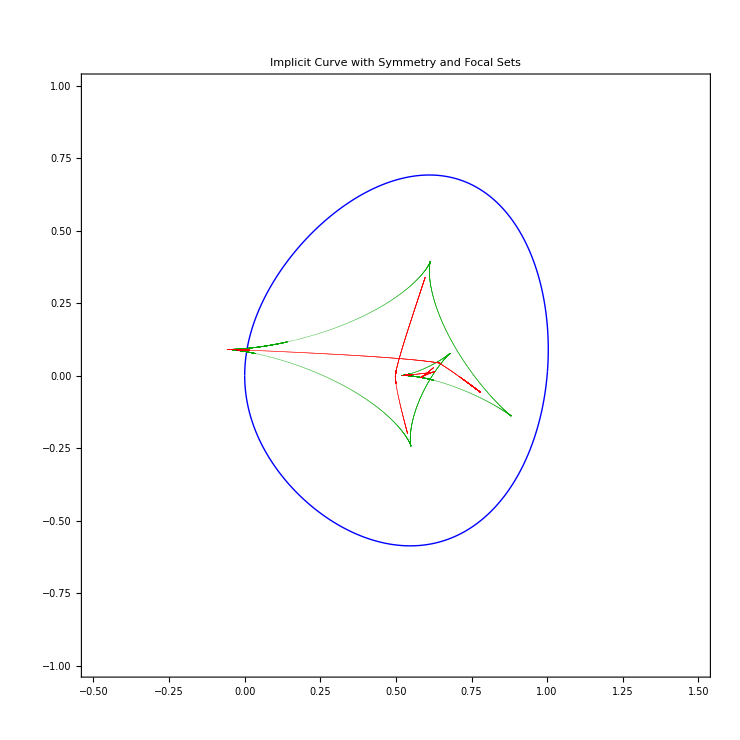

```mathematica
(*(*Plot all together*)
(*Import the data*)data=Import["potato_plot.csv"];

(*Parse the data*)
curvePoints=Select[data[[2;;]],#[[1]]=="curve"&][[All,2;;3]];
symmetryPoints=Select[data[[2;;]],#[[1]]=="symmetry"&][[All,2;;3]];
focalPoints=Select[data[[2;;]],#[[1]]=="focal"&][[All,2;;3]];*)

plot=Show[ListPlot[curvePoints,PlotStyle->{Blue,Thick},Joined->True,PlotLegends->Placed[{"Curve"},{Right,Top}]],ListPlot[focalPoints,PlotStyle->{Darker[Green],PointSize[0.000001]},PlotLegends->Placed[{"Focal Set"},{Right,Top}]],ListPlot[symmetryPoints,PlotStyle->{Red,PointSize[0.000001]},PlotLegends->Placed[{"Symmetry Set"},{Right,Top}]],PlotRange->{{-0.5,1.5},{-1,1}},AspectRatio->Automatic,Frame->True,PlotLabel->"Implicit Curve with Symmetry and Focal Sets",ImageSize->1000,Axes->False]
```

```mathematica
circleCenter={0.628755,0.013425};
r=0.011;
numPoints=200;
circlePlot=Graphics[{EdgeForm[{Red,Dashed,Thick}],FaceForm[None],Circle[circleCenter,r]}];

angles=Table[theta,{theta,0,2*Pi-(2*Pi)/numPoints,(2*Pi)/numPoints}];

sampledCirclePoints=Table[circleCenter+r*{Cos[a],Sin[a]},{a,angles}];

sampledPointsPlot=ListPlot[sampledCirclePoints,PlotStyle->{Black,PointSize[0.001],AbsoluteThickness[.0001],Directive[CapForm["Butt"],AbsoluteThickness[1]],PlotMarkers->Graphics[{Line[{{-1,0},{1,0}}],Line[{{0,-1},{0,1}}]}] },PlotLegends->Placed[{"Sampled Points"},{Right,Top}]];

plot=Show[ListPlot[curvePoints,PlotStyle->{Blue,Thick},Joined->True,PlotLegends->Placed[{"Curve"},{Right,Top}]],ListPlot[focalPoints,PlotStyle->{Darker[Green],PointSize[0.000001]},PlotLegends->Placed[{"Focal Set"},{Right,Top}]],ListPlot[symmetryPoints,PlotStyle->{Red,PointSize[0.000001]},PlotLegends->Placed[{"Symmetry Set"},{Right,Top}]],circlePlot,sampledPointsPlot,
(*Plot range here*)PlotRange->{{0.45,0.75},{-0.1,0.1}},AspectRatio->Automatic,Frame->True,PlotLabel->"Implicit Curve with Symmetry and Focal Sets",ImageSize->1000,Axes->False]
```

```mathematica
(*Parse the data*)
curvePoints=Select[data[[2;;]],#[[1]]=="curve"&][[All,2;;3]];
symmetryPoints=Select[data[[2;;]],#[[1]]=="symmetry"&][[All,2;;3]];
focalPoints=Select[data[[2;;]],#[[1]]=="focal"&][[All,2;;3]];
```

```mathematica
Export["potato_plot_zoom.pdf",plot]
```

potato_plot_zoom.pdf

```mathematica
SystemOpen["potato_plot_zoom.pdf"]
```

```mathematica
formattedCurve=Insert[#,"curve",1]&/@curvePoints;
formattedFocal=Insert[#,"focal",1]&/@focalPoints;
formattedSymmetry=Insert[#,"symmetry",1]&/@symmetryPoints;

(*Combine all data into one big list*)
allData=Join[formattedCurve,formattedFocal,formattedSymmetry];

(*Add a header row for clarity in the CSV*)
header={"Type","X","Y"};
exportData=Prepend[allData,header];
Export["potato_plot.csv",exportData]
```

potato_plot.csv

```mathematica
header={"X","Y"};
exportData=Prepend[sampledCirclePoints,header];
Export["potato_circle_points.csv",exportData]
```

potato_circle_points.csv

## Plotting from csv

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/roroy/Desktop/Code/symmetry_set

```mathematica
(*Import the data*)data=Import["potato_plot.csv"];

(*Parse the data*)
curvePoints=Select[data[[2;;]],#[[1]]=="curve"&][[All,2;;3]];
symmetryPoints=Select[data[[2;;]],#[[1]]=="symmetry"&][[All,2;;3]];
focalPoints=Select[data[[2;;]],#[[1]]=="focal"&][[All,2;;3]];

(*Create animation frames*)
totalSymmetryPoints=Length[symmetryPoints];
totalFocalPoints=Length[focalPoints];

(*Determine plot range from all data*)
allPoints=Join[curvePoints,symmetryPoints,focalPoints];
xRange={Min[allPoints[[All,1]]],Max[allPoints[[All,1]]]};
yRange={Min[allPoints[[All,2]]],Max[allPoints[[All,2]]]};
padding=0.5;
plotRange={{xRange[[1]]-padding,xRange[[2]]+padding},{yRange[[1]]-padding,yRange[[2]]+padding}};

(*Create animation-plotting symmetry and focal points progressively*)
frames=Table[Show[(*Always show the full curve*)ListPlot[curvePoints,PlotStyle->{Blue,Thick},Joined->True],(*Show symmetry points up to frame i*)If[i≤totalSymmetryPoints,ListPlot[symmetryPoints[[1;;i]],PlotStyle->{Red,PointSize[0.008]}],ListPlot[symmetryPoints,PlotStyle->{Red,PointSize[0.008]}]],(*Show focal points after symmetry points are done*)If[i>totalSymmetryPoints,ListPlot[focalPoints[[1;;Min[i-totalSymmetryPoints,totalFocalPoints]]],PlotStyle->{Green,PointSize[0.008]}],Graphics[{}]],PlotRange->plotRange,AspectRatio->Automatic,Frame->True,PlotLabel->If[i≤totalSymmetryPoints,StringForm["Symmetry Set: `` / `` points",i,totalSymmetryPoints],StringForm["Symmetry: `` | Focal: `` / ``",totalSymmetryPoints,i-totalSymmetryPoints,totalFocalPoints]],ImageSize->600],{i,1,totalSymmetryPoints+totalFocalPoints,Max[1,Floor[(totalSymmetryPoints+totalFocalPoints)/200]]}];

(*Export as animated GIF*)
Export["potato_symmetry_animation.gif",frames,"DisplayDurations"->0.05,"AnimationRepetitions"->Infinity];

Print["Animation created!"];
Print["Total symmetry points: ",totalSymmetryPoints];
Print["Total focal points: ",totalFocalPoints];

(*Also create a final static plot*)
finalPlot=Show[ListPlot[curvePoints,PlotStyle->{Blue,Thick},Joined->True,PlotLegends->{"Curve"}],ListPlot[symmetryPoints,PlotStyle->{Red,PointSize[0.006]},PlotLegends->{"Symmetry Set"}],ListPlot[focalPoints,PlotStyle->{Green,PointSize[0.006]},PlotLegends->{"Focal Set"}],PlotRange->plotRange,AspectRatio->Automatic,Frame->True,PlotLabel->"Complete Symmetry and Focal Sets",ImageSize->700];

Export["potato_complete_plot.png",finalPlot];

Print["Static plot saved!"];
```

Animation created!

Total symmetry points: 1599

Total focal points: 1599

Static plot saved!

#### Implicit equations

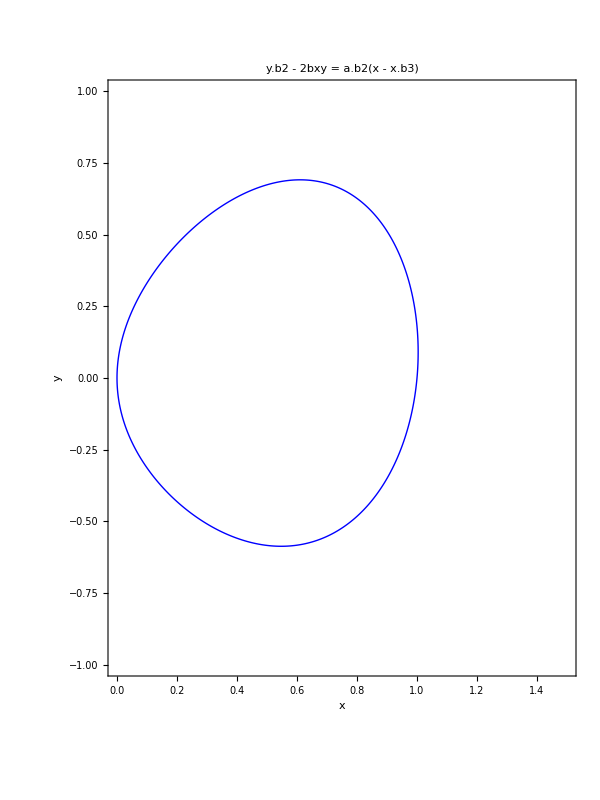

```mathematica
m=1.025;
p=0.09;
ContourPlot[y^2-2 p x y==m^2(x-x^3), {x,0,1.5}, {y,-1,1},ContourStyle->{Blue,Thick},AspectRatio->Automatic,Frame->True,FrameLabel->{"x","y"},PlotLabel->"y.b2 - 2bxy = a.b2(x - x.b3)",ImageSize->600,PlotPoints->100]
```

#### Spiral

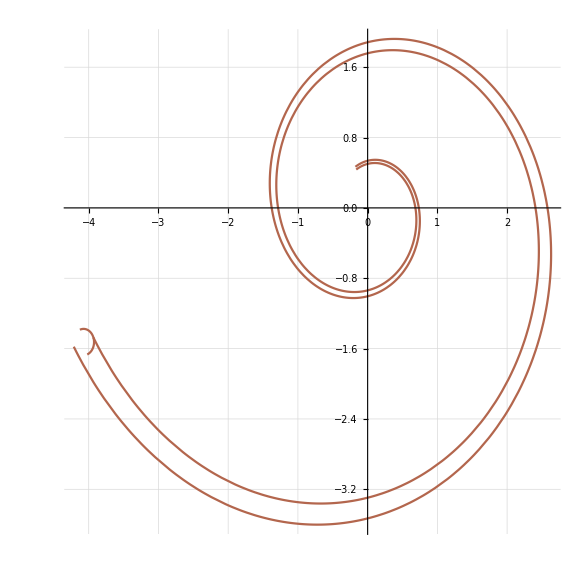

```mathematica
(*---1. Clear all previous definitions---*)Clear["Global`*"];

(*---2. Define Parameters for an INWARD spiral---*)
b=0.2;(*Growth rate (controls "tightness")*)tmin=3.5;(*Starting angle (t) in radians-This is the OUTER end*)tmax=tmin+3.5*Pi;(*Ending angle (t)-This is the INNER end*)(*---We want the outer radii to be a certain size at tmin---*)(*Let's set the outer radius (R) and thickness*)ROuter=4.5;(*Desired radius of the outer-most curve at the start*)thickness=0.3;(*Desired thickness of the hollow shape*)RInner=ROuter-thickness;

(*---Calculate the'a' scaling factors to get these radii---*)
(*R=a*Exp[-b*tmin]=>a=R*Exp[b*tmin]*)
aOuter=ROuter*Exp[b*tmin];
aInner=RInner*Exp[b*tmin];

(*---3. Define the INWARD Spiral Equations---*)
(*Note the Exp[-b*t] to spiral INWARDS*)
innerSpiral[t_]:={aInner*Exp[-b*t]*Cos[t],aInner*Exp[-b*t]*Sin[t]}
outerSpiral[t_]:={aOuter*Exp[-b*t]*Cos[t],aOuter*Exp[-b*t]*Sin[t]}

(*---4. Define the Rounded End Cap (at the start,t=tmin)---*)
p1=innerSpiral[tmin];
p2=outerSpiral[tmin];
center=(p1+p2)/2;
radius=Norm[p2-p1]/2;
endCap[s_]:=center+radius*{Cos[s+tmin+Pi/2],Sin[s+tmin+Pi/2]}

(*---5. Generate the Plots---*)
plotInner=ParametricPlot[innerSpiral[t],{t,tmin,tmax},PlotStyle->RGBColor[0.7,0.4,0.3]];

plotOuter=ParametricPlot[outerSpiral[t],{t,tmin,tmax},PlotStyle->RGBColor[0.7,0.4,0.3]];

plotCap=ParametricPlot[endCap[s],{s,0,Pi},PlotStyle->RGBColor[0.7,0.4,0.3]];

(*---6. Combine and Style Everything---*)
Show[{plotInner,plotOuter,plotCap},GridLines->Automatic,GridLinesStyle->LightGray,Axes->True,AxesOrigin->{0,0},AxesStyle->{Red,Green},Frame->False,AspectRatio->1,PlotRange->All]
```

```mathematica
b=0.2;
tmin=3.5;
tmax=tmin+3.5*Pi;
ROuter=4.5;
thickness=0.3;
RInner=ROuter-thickness;

aOuter=ROuter*Exp[b*tmin];
aInner=RInner*Exp[b*tmin];

innerSpiral[t_]:={aInner*Exp[-b*t]*Cos[t],aInner*Exp[-b*t]*Sin[t]}
outerSpiral[t_]:={aOuter*Exp[-b*t]*Cos[t],aOuter*Exp[-b*t]*Sin[t]}
```